```mathematica
s=Import["/home/vladimir/Documents/Courses/Técnicas/Espectro de transmitancia.xlsx"][[1]];
```

```mathematica
λ = s[[2;;-1,1]];
Subscript[T, P] = s[[2;;-1,2]];
Subscript[T, V] = s[[2;;-1, 3]];
```

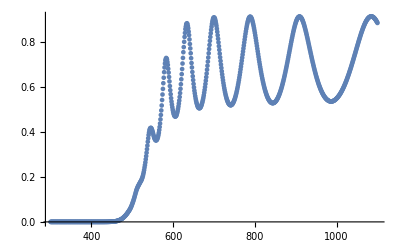

```mathematica
data=Transpose@{λ, Subscript[T, P]};
ListPlot[data]
```

```mathematica
windowMin[data_,w_][pt_]:={pt,Min[Cases[data,{x_,y_}/;pt-w≤x≤pt+w][[All,2]]]}

windowMax[data_,w_][pt_]:={pt,Max[Cases[data,{x_,y_}/;pt-w≤x≤pt+w][[All,2]]]}
```

```mathematica
f[xdata_,ydata_,w_]/;Length[xdata]==Length[ydata]:=Block[{data=Transpose[{xdata,ydata}],xmin=Min[xdata],xmax=Max[xdata]},Show[ListLinePlot[data,PlotStyle->Directive[{Blue,Opacity[.2]}]],With[{pts=Table[windowMin[data,w][t],{t,xmin,xmax,w-w/(xmax-xmin)}]},Graphics[{Red,BSplineCurve[pts]}]],With[{pts=Table[windowMax[data,w][t],{t,xmin,xmax,w-w/(xmax-xmin)}]},Graphics[{Red,BSplineCurve[pts]}]]]]
```

```mathematica
f[ λ, Subscript[T, P], 40]
```

-Graphics-